# Analytics of the L1 points (x in [0,1])

Author : Martin Horvat, March 2016

## Definitions

```mathematica
(* Omega = delta*KopalPotential(x = delta t, y=0, z=0), a = F^2 delta^3 *)
Clear[Omega];
Omega[t_]:=1/Abs[t]+q(1/Abs[1-t] -t)+1/2 a(1+q) t^2

(* Omega1 is Omega for t in [0,1] *)
Clear[Omega1];
Omega1[t_]:=1/t+q(1/(1-t) - t)+1/2 a(1+q) t^2

(* Derivative Omega1 *)
Clear[dOmega1];
dOmega1[t_]=Together[D[Omega1[t],t]]
```

(-1+2 t-t^2+a t^3+2 q t^3+a q t^3-2 a t^4-q t^4-2 a q t^4+a t^5+a q t^5)/((-1+t)^2 t^2)

```mathematica
(* Polynomials *)
```

```mathematica
Clear[P];
P[t_,q_,a_]=Simplify[-Numerator[dOmega1[t]]]
```

1-2 t+t^2-(a+2 q+a q) t^3+(q+2 a (1+q)) t^4-a (1+q) t^5

```mathematica
Clear[Q];
Q[s_,q_,a_]=Simplify[-Numerator[Together[dOmega1[s/(1+s)]]]]
```

1+3 s+3 s^2-(-1+a+2 q+a q) s^3-3 q s^4-q s^5

```mathematica
(* Solution *)
```

```mathematica
Clear[Sol]
Sol[q_,a_]:=Module[{t},First[t/.Solve[{P[t,q,a]==0,0<t<1},t,Reals]]];
```

```mathematica
HornerForm[P[x,q,a]/.a ->b/(1+q),x]
```

1+x (-2+x (1+x (-b-2 q+x (2 b+q-b x))))

```mathematica
HornerForm[D[P[x,q,a]/.a ->b/(1+q),x],x]
```

-2+x (2+x (-3 b-6 q+x (8 b+4 q-5 b x)))

## Plots

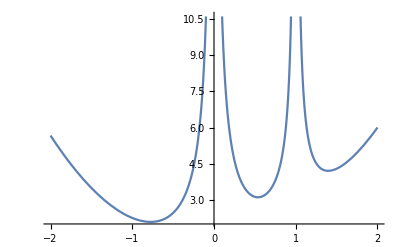

```mathematica
Plot[Omega[t]/.{q->0.5,a->2},{t,-2,2}]
```

## a = 1

Using Q: 
	t=s/(1+s)
	q->infty: 
		w =(3q)^(-1/3), 
		t= s/(1+s),
		z=3 w^3 = 1/q,
		s=S1[w];
	q->0:
		w= (q/3)^(1/3),
		t=1/(1+s),
		z=3 w^3 =q,
		s = S1[w];

```mathematica
S1[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[(3+3 s+s^2)/(1+3 s+3 s^2)s^3,{s,0,12}],z]]/.z->3w^3,w>0],{w,0,8}]]
```

w+(2 w^2)/3+(2 w^3)/9-(32 w^4)/81-(50 w^5)/243+(2 w^6)/9+(3080 w^7)/6561-(5330 w^8)/19683

```mathematica
(* Checking *)
Block[{w,q,s},
q=10.;
w=(3*q)^(-1/3);
s=S1[w];
{s/(1+s),Sol[q,1]}
]
```

{0.282497,0.282487}

```mathematica
(* Checking *)
Block[{w,q,s},
q=0.1;
w=(q/3)^(1/3);
s=S1[w];
{1/(1+s),Sol[q,1]}
]
```

{0.717503,0.717513}

Using Q : q->1	
    q =1 + e
    s=1 + u
  
  t= s/(1+s)
  u=U1[e]
  
  t=(1+u)/(2+u)

```mathematica
U1[e_]=Normal[InverseSeries[Series[((3+3 s+s^2)/(1+3 s+3 s^2)s^3/.s->1+u)-1,{u,0,8}],e]]
```

(7 e)/17-(35 e^2)/289+(5229 e^3)/83521-(56574 e^4)/1419857+(11609304 e^5)/410338673-(149902998 e^6)/6975757441+(34436990322 e^7)/2015993900449-(480838216341 e^8)/34271896307633

```mathematica
(* Checking *)
Block[{q,e,u},
q=1.1;
e=q-1;
u=U1[e];
{(1+u)/(2+u),Sol[q,1]}
]
```

{0.50981,0.49019}

Using P : q->1	
    q =1 + e
    t=1/2 + u
  
  u=U2[e]
  
  t=1/2+u

```mathematica
U2[e_]=Normal[InverseSeries[Series[(((1-t)^3(1+t+t^2))/(t^3(3-3 t+ t^2))/.t->1/2+u)-1,{u,0,8}],e]]
```

-(7 e)/68+(7 e^2)/136-(43407 e^3)/1336336+(61439 e^4)/2672672-(457865807 e^5)/26261675072+(727564943 e^6)/52523350144-(5872650172767 e^7)/516094438514944+(9893062421599 e^8)/1032188877029888

```mathematica
(* Checking *)
Block[{q,e,u},
q=1.1;
e=q-1;
u=U2[e];
{1/2+U2[e],Sol[q,1]}
]
```

{0.49019,0.49019}

## q=1

### a →0

Using P : a ->0
t = t0 +u 	where 	P(t0,q=1,a=0) = 0

```mathematica
P1[t_]=P[t,1,0]
P2[t_]=Simplify[D[P[t,1,a],a]]
```

1-2 t+t^2-2 t^3+t^4

-2 (-1+t)^2 t^3

```mathematica
t01=Simplify[t/.Solve[P1[t]==0,t][[1]]]
```

1/2 (1+√2-√(-1+2 √2))

```mathematica
U3[a_]=N[Normal[InverseSeries[Series[-P1[t01+u]/P2[t01+u],{u,0,8}],a]]]
```

-0.0324324 a+0.00120098 a^2+0.000266773 a^3-0.0000442423 a^4-2.60169×10^-6 a^5+1.50975×10^-6 a^6-6.68804×10^-8 a^7-4.43826×10^-8 a^8

```mathematica
Rest[CForm/@CoefficientList[U3[a],a]]
```

{-0.032432373069687326,0.0012009812247423704,0.00026677335735642835,-0.000044242336209068785,-2.6016936984989166e-6,1.5097474266330576e-6,-6.688040686774399e-8,-4.438264579211867e-8}

```mathematica
HornerForm[Sum[c[i-1]a^i,{i,1,8}],a]
```

a (c[0]+a (c[1]+a (c[2]+a (c[3]+a (c[4]+a (c[5]+a (c[6]+a c[7])))))))

```mathematica
Block[{a},
a=0.1;
{t01+U3[a],Sol[1,a]}
]
```

{0.527779,0.527779}

### a → ∞

Using Q : a ->infty
s = u
w=(2a)^(-1/3)
t=s/(1+s)

```mathematica
Q1[s_]=Q[s,1,0]
Q2[s_]=Simplify[D[Q[s,1,a],a]]
```

1+3 s+3 s^2-s^3-3 s^4-s^5

-2 s^3

```mathematica
S2[w_]=Normal[Series[Simplify[Normal[InverseSeries[Series[-Q2[s]/(2Q1[s]),{s,0,12}],z]]/.z->w^3,w>0],{w,0,8}]]
```

w+w^2+w^3+w^4/3-(4 w^5)/3-(13 w^6)/3-(73 w^7)/9-(91 w^8)/9

```mathematica
HornerForm[S2[w],w]
```

w (1+w (1+w (1+w (1/3+w (-4/3+w (-13/3+(-73/9-(91 w)/9) w))))))

```mathematica
Block[{a,w,s},
a=6.;
w=(2a)^(-1/3);
s=S2[w];
{s/(1+s),Sol[1,a]}
]
```

{0.387912,0.393828}

### a ≈ 1

Using P : a  approx 1
t =1/2 + u
a=1 + e

```mathematica
U4[e_]=Normal[InverseSeries[Series[-P1[1/2+u]/P2[1/2+u]-1,{u,0,8}],e]]
```

-e/34+e^2/578+(15 e^3)/167042-(111 e^4)/2839714+(2895 e^5)/820677346+(6017 e^6)/13951514882-(649377 e^7)/4031987800898+(896945 e^8)/68543792615266

```mathematica
Block[{a,e,u},
a=1.5;
e=a-1;
u=U4[e];
{1/2+u,Sol[1,a]}
]
```

{0.485736,0.485736}

```mathematica
CForm/@Rest[CoefficientList[U4[e],e]]
```

{-0.029411764705882353,0.0017301038062283738,0.00008979777540977718,-0.00003908844341366772,3.5275739169727247e-6,4.3127933065985745e-7,-1.610562908586607e-7,1.3085721781321937e-8}

## a != 1, q!=1

### a -> ∞

Using Q : a  -> infty
t=s/(1+s)

Q=0 : (1+s)^3 - c s^3 -q s^4(3+s) = 0	c= a + q(2+a)

1/c = s^3/((1+s)^3 - q s^4(3+s)) = w^3

```mathematica
S3[w_]=Normal[Series[Normal[InverseSeries[Series[s^3/((1+s)^3-q s^4(3+s)),{s,0,12}],z]]/.z->w^3,{w,0,8}]]
```

w+w^2+w^3+w^4+(1-q) w^5+(1-(10 q)/3) w^6+(1-(22 q)/3) w^7+(1-(40 q)/3) w^8

```mathematica
HornerForm[S3[w],w]
```

w (1+w (1+w (1+w (1+w (1-q+w (1-(10 q)/3+w (1-(22 q)/3+(1-(40 q)/3) w)))))))

```mathematica
Block[{a,c,w,s,q},
a=2.;
q=0.1;
c=2q+a(1+q);
w=c^(-1/3);

s=S3[w];
{s,s/(1+s),Sol[q,a]}
]
```

{2.35987,0.702369,0.665504}

Tunning:

Using Q : a  -> infty
t=s/(1+s)

Q=0 : (1+s)^3 +k s^3 - c s^3 -q s^4(3+s) = 0	c= a + q(2+a) +k

1/c = s^3/((1+s)^3 +k s^3 - q s^4(3+s)) = w^3

```mathematica
S31[w_]=Normal[Series[Normal[InverseSeries[Series[s^3/((1+s)^3+k s^3-q s^4(3+s)),{s,0,12}],z]]/.z->w^3,{w,0,8}]]
```

w+w^2+w^3+(1+k/3) w^4+(1+(2 k)/3-q) w^5+(1+k-(10 q)/3) w^6+1/9 (9+12 k+2 k^2-66 q) w^7+1/9 (9+15 k+5 k^2-120 q-15 k q) w^8

```mathematica
Block[{a,c,w,s,q,kk},
a=1000.;
q=10;
kk=-1;
c=kk+2q+a(1+q);
w=c^(-1/3);

s=S31[w]/.k->kk;
{s,s/(1+s),Sol[q,a]}
]
```

{0.0470494,0.0449353,0.0449353}

```mathematica
HornerForm[S31[w],w]/.k->-1
CForm[%]
```

w (1+w (1+w (1+w (2/3+w (1/3-q+w (-(10 q)/3+w (-1/9-(22 q)/3+(-1/9-(35 q)/3) w)))))))

w*(1 + w*(1 + w*(1 + w*(0.6666666666666666 + w*(0.3333333333333333 - q + 
                 w*((-10*q)/3. + w*(-0.1111111111111111 - (22*q)/3. + (-0.1111111111111111 - (35*q)/3.)*w)))))))

### q -> ∞

Using Q : q  -> infty
t=s/(1+s)

Q=0 : 1/q = s^3 (2 + a + 3 s + s^2)/(1+3s+3s^2+(1-a)s^3) = (2+a)w^3

w=((2+a) q)^(-1/3)

```mathematica
S4[w_]=Normal[Simplify[Series[Simplify[Normal[InverseSeries[Series[(2+a+3 s+s^2)/(1+3 s+3 s^2-(a-1)s^3)s^3,{s,0,12}],z]]/.z->(2+a)w^3,w>0&&a>0],{w,0,8}]]]
```

w+((1+a) w^2)/(2+a)+((1+2 a+3 a^2) w^3)/(3 (2+a)^2)-((1+11 a+16 a^2+3 a^3+a^4) w^4)/(3 (2+a)^3)-(2 (1-8 a+16 a^2+51 a^3+12 a^4+3 a^5) w^5)/(9 (2+a)^4)+((1+13 a+88 a^2+92 a^3-22 a^4-7 a^5-3 a^6) w^6)/(3 (2+a)^5)+((20-240 a-264 a^2+8386 a^3+14265 a^4+4176 a^5+1251 a^6+108 a^7+18 a^8) w^7)/(81 (2+a)^6)+((-35-581 a-10176 a^2-36445 a^3-25084 a^4+14898 a^5+6402 a^6+2691 a^7+315 a^8+45 a^9) w^8)/(81 (2+a)^7)

```mathematica
Block[{a,w,s,q},
a=1.;
q=10;
w=((2+a)q)^(-1/3);

s=S4[w];
{s/(1+s),Sol[q,a]}
]
```

{0.282497,0.282487}

```mathematica
div1={1,1,3,3,-9/2,3,81,81};
HornerForm/@(Rest[CoefficientList[Normal[Series[S4[z*(2+a)]/(2+a),{z,0,8}]],z]] *div1)
```

{1,1+a,1+a (2+3 a),-1+a (-11+a (-16+(-3-a) a)),1+a (-8+a (16+a (51+a (12+3 a)))),1+a (13+a (88+a (92+a (-22+(-7-3 a) a)))),20+a (-240+a (-264+a (8386+a (14265+a (4176+a (1251+a (108+18 a))))))),-35+a (-581+a (-10176+a (-36445+a (-25084+a (14898+a (6402+a (2691+a (315+45 a))))))))}

### a->0

Using P : a  -> 0

P=0: R(t) := ((1-t)^2 + qt^3(t-2))/(t^3(1-t)^2) = b := a(1+q)

R(t0)=0 : (1-t_0)^2 + qt_0^3(t_0-2) = 0

t=t0+u

```mathematica
P[t,q,a]
```

1-2 t+t^2-(a+2 q+a q) t^3+(q+2 a (1+q)) t^4-a (1+q) t^5

```mathematica
R1[t_,q_]:=((1-t)^2+q t^3(t-2))/(t^3(1-t)^2)
```

```mathematica
C1[q_]=t/.Solve[(1-t)^2+q t^3(t-2)==0,t];
```

```mathematica
t02[q_]=C1[q][[3]]
```

1/2+(√(3-2/q+1/(q (1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))/q))/(2 √3)-1/2 √(2-4/(3 q)-1/(3 q (1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))-((1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))/(3 q)+(√3 (8+8/q))/(4 √(3-2/q+1/(q (1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))+((1+54 q^2+6 √3 √(q^2+27 q^4))^(1/3))/q)))

```mathematica
Simplify[t02[q]/.(1+54 q^2+6 √3 √(q^2+27 q^4))->f1^3,f1>0]/.{√((1-2 f1+f1^2+3 f1 q)/(f1 q))->f2,1/√((1-2 f1+f1^2+3 f1 q)/(f1 q))->1/f2}
```

1/6 (3+√3 f2-√3 √(6-4/q-1/(f1 q)-f1/q+(6 √3 (1+q))/(f2 q)))

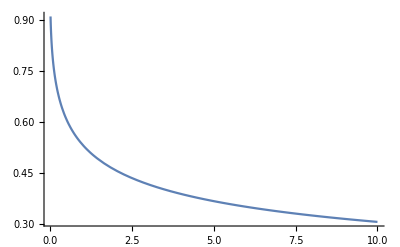

```mathematica
Plot[t02[q],{q,0.01,10},PlotRange->All]
```

```mathematica
DR1[t_,q_]=FullSimplify[Table[D[R1[t,q],{t,n}]/n!,{n,1,8}],q>0]
```

{-(q (-3+t))/(-1+t)^3-3/t^4,(q (-4+t))/(-1+t)^4+6/t^5,-(q (-5+t))/(-1+t)^5-10/t^6,(q (-6+t))/(-1+t)^6+15/t^7,-(q (-7+t))/(-1+t)^7-21/t^8,(q (-8+t))/(-1+t)^8+28/t^9,-(q (-9+t))/(-1+t)^9-36/t^10,(q (-10+t))/(-1+t)^10+45/t^11}

```mathematica
Block[{r,A,B,Bc},
r[0]=1;

A=With[{n=8},SeriesData[x,0,Array[r,n,0],1,n+1,1]];
B=InverseSeries[A,x];
Bc=CoefficientList[B,x];
Print[A];
Print[B];
HornerForm/@Print[Bc]
]
```

x+r[1] x^2+r[2] x^3+r[3] x^4+r[4] x^5+r[5] x^6+r[6] x^7+r[7] x^8+O[x]^9

x-r[1] x^2+(2 r[1]^2-r[2]) x^3+(-5 r[1]^3+5 r[1] r[2]-r[3]) x^4+(14 r[1]^4-21 r[1]^2 r[2]+3 r[2]^2+6 r[1] r[3]-r[4]) x^5+(-42 r[1]^5+84 r[1]^3 r[2]-28 r[1] r[2]^2-28 r[1]^2 r[3]+7 r[2] r[3]+7 r[1] r[4]-r[5]) x^6+(132 r[1]^6-330 r[1]^4 r[2]+180 r[1]^2 r[2]^2-12 r[2]^3+120 r[1]^3 r[3]-72 r[1] r[2] r[3]+4 r[3]^2-36 r[1]^2 r[4]+8 r[2] r[4]+8 r[1] r[5]-r[6]) x^7+(-429 r[1]^7+1287 r[1]^5 r[2]-990 r[1]^3 r[2]^2+165 r[1] r[2]^3-495 r[1]^4 r[3]+495 r[1]^2 r[2] r[3]-45 r[2]^2 r[3]-45 r[1] r[3]^2+165 r[1]^3 r[4]-90 r[1] r[2] r[4]+9 r[3] r[4]-45 r[1]^2 r[5]+9 r[2] r[5]+9 r[1] r[6]-r[7]) x^8+O[x]^9

{0,1,-r[1],2 r[1]^2-r[2],-5 r[1]^3+5 r[1] r[2]-r[3],14 r[1]^4-21 r[1]^2 r[2]+3 r[2]^2+6 r[1] r[3]-r[4],-42 r[1]^5+84 r[1]^3 r[2]-28 r[1] r[2]^2-28 r[1]^2 r[3]+7 r[2] r[3]+7 r[1] r[4]-r[5],132 r[1]^6-330 r[1]^4 r[2]+180 r[1]^2 r[2]^2-12 r[2]^3+120 r[1]^3 r[3]-72 r[1] r[2] r[3]+4 r[3]^2-36 r[1]^2 r[4]+8 r[2] r[4]+8 r[1] r[5]-r[6],-429 r[1]^7+1287 r[1]^5 r[2]-990 r[1]^3 r[2]^2+165 r[1] r[2]^3-495 r[1]^4 r[3]+495 r[1]^2 r[2] r[3]-45 r[2]^2 r[3]-45 r[1] r[3]^2+165 r[1]^3 r[4]-90 r[1] r[2] r[4]+9 r[3] r[4]-45 r[1]^2 r[5]+9 r[2] r[5]+9 r[1] r[6]-r[7]}

```mathematica
Block[{a,b,n,t0,x,q,w,dR,u},
q=10.;
a=2.;
b= a*(1+q);

t0=t02[q];
dR=DR1[t0,q];

w=N[b/dR[[1]]];
dR/=dR[[1]];

n=8;
u=Normal[InverseSeries[SeriesData[x,0,dR,1,n+1,1],x]]/.x->w;

{t0,t0+u,Sol[q,a]}
]
```

{0.305361,0.264443,0.26444}

Comment : Work well for small a, but q far away from 0, fnite size, lets say.

### q->0

Using P = 0 in limit q -> 0 expressed in the form

	q= (1-t)^2/t^3 (1-b t^3)/(2-t)

with b = a(1+q) or

	q = (1 - t)^2 (1 - ct) R (t) 

	R (t) = (1 + (ct)^2 + (ct)^2)/(t^3 (2 - t))

where c = (a (1 + q))^(1/3). It is solved by iteration

	q/R (t_ {n - 1}) = (1 - t_n)^2 (1 - c t_n)
	
Convergence is usually good for small q < 0.5 and best for c > 1

```mathematica
(* Solving equation (1-t)^2 (1-s t) = z*)
SolveCubic1[s_,z_]:=Module[{b,c,d,p,q,A,phi,dd,sd,t},
If[s==1,Return[1-z^(1/3)]];

b=-2-1/s;
c=1+2/s;
d=(z-1)/s;

p=c-b^2/3;
q=d+b(2b^2/27-c/3);

dd=p^3/27+q^2/4;
A=2*Sqrt[Abs[p]/3];

If[dd≤0,
phi=ArcCos[3*q/(A*p)]-4Pi;
Return[A*Cos[phi/3]-b/3];
];

If [p<0,
phi=ArcCosh[-3*Abs[q]/(A*p)];
Return[-A*Sign[q]Cosh[phi/3]-b/3];
];

phi=ArcSinh[3*q/(A*p)];
Return[-A*Sinh[phi/3]-b/3]
];

SolveCubic2[s_,z_]:=Module[{t},First[t/.Solve[{(1-t)^2 (1-s t)==z,0<t<1},t,Reals]]]
```

```mathematica
R2[t_,c_]:=(1+(c t)+(c t)^2)/(t^3(2-t));
```

```mathematica
Block[{a,q,c,m,t},
a=1.;
q=0.5;
c=(a(1+q))^(1/3);

t=If[c>1, 1/c,1];

m=4;
Do[
t=SolveCubic1[c,q/R2[t,c]],
{m}
];

{t,Sol[q,a]}
]
```

{0.577838,0.570752}

```mathematica
Block[{b,c,d,p,q,s},
b=-2-1/s;
c=1+2/s;
d=(z-1)/s;

p=c-b^2/3;
q=d+b(2b^2/27-c/3);

FullSimplify[{p,q,p^3/27+q^2/4}]
]
```

{-(-1+s)^2/(3 s^2),(2 (-1+s)^3)/(27 s^3)+z/s,(z (4 (-1+s)^3+27 s^2 z))/(108 s^4)}

### a ≈ 1

Using P and expressing P=0 around a=1 in the form:
  
  R (t) := P (t, q, a = 1)/(t^3 (1 - t)^2) = (1 + q) (a - 1)
  
Good approximation for a large range around a = 1 and q > 0.1

```mathematica
Simplify[P[t,q,a]-P[t,q,1]]
```

-(-1+a) (1+q) (-1+t)^2 t^3

```mathematica
R3[t_,q_]:=P[t,q,1]/(t^3(1-t)^2);
```

```mathematica
Simplify[R3[t,q]-R1[t,q]]
```

-1-q

```mathematica
DR2[t_,q_]=FullSimplify[Table[D[R3[t,q],{t,n}]/n!,{n,1,8}],q>0]
```

{-(q (-3+t))/(-1+t)^3-3/t^4,(q (-4+t))/(-1+t)^4+6/t^5,-(q (-5+t))/(-1+t)^5-10/t^6,(q (-6+t))/(-1+t)^6+15/t^7,-(q (-7+t))/(-1+t)^7-21/t^8,(q (-8+t))/(-1+t)^8+28/t^9,-(q (-9+t))/(-1+t)^9-36/t^10,(q (-10+t))/(-1+t)^10+45/t^11}

```mathematica
DR1[t,q]
```

{-(q (-3+t))/(-1+t)^3-3/t^4,(q (-4+t))/(-1+t)^4+6/t^5,-(q (-5+t))/(-1+t)^5-10/t^6,(q (-6+t))/(-1+t)^6+15/t^7,-(q (-7+t))/(-1+t)^7-21/t^8,(q (-8+t))/(-1+t)^8+28/t^9,-(q (-9+t))/(-1+t)^9-36/t^10,(q (-10+t))/(-1+t)^10+45/t^11}

```mathematica
Block[{a,b,n,t0,x,q,w,dR,u},
q=2.;
a=4;
b= (a-1)*(1+q);

t0=Sol[q,1];(* !!! *)
dR=DR2[t0,q];

w=N[b/dR[[1]]];
dR/=dR[[1]];

n=8;
u=Normal[InverseSeries[SeriesData[x,0,dR,1,n+1,1],x]]/.x->w;

{t0,t0+u,Sol[q,a]}
]
```

{0.429248,0.367463,0.367427}